## main

```mathematica
thisfolder=NotebookDirectory[];
rootfolder=StringSplit[thisfolder,"/"][[1;;Length[StringSplit[thisfolder,"/"]]-1]];
rootfolder=StringJoin[StringJoin[Flatten[Table[{"/",rootfolder[[j]]},{j,1,Length[rootfolder]}]]],"/"];
model=Import[StringJoin[thisfolder,"main_output.jam"],"Table"];
data=Import[StringJoin[thisfolder,"seriesP.jam"],"Table"];
model=Table[{model[[i,1]],model[[i,2]],model[[i,3]],data[[i,4]],model[[i,4]]},{i,1,Length[model]}];
epochs=Union[model[[All,4]]];
OOTs=Table[Max[Select[model,#[[4]]==epochs[[i]]&][[All,5]]],{i,1,Length[epochs]}];
j=0;Label[jloop];j=j+1;Subscript[mini, j]=Select[model,#[[4]]==epochs[[j]]&];If[j<Length[epochs],Goto[jloop]];
```

```mathematica
temp=Flatten[Import[StringJoin[NotebookDirectory[],"bestmode.jam"],"Table"]];
Pdays=temp[[4]]
τ0=temp[[5]]
Msptrue=temp[[13]]
strue=temp[[14]] temp[[1]]
```

59.9888

0

0.0314645

0.0183154

```mathematica
σ=Max[1.4286MedianDeviation[Table[model[[i,2]]-model[[i,5]],{i,1,Length[model]}]],Median[model[[All,3]]]];
f=3;
xwidth=Max[Table[Max[Subscript[mini, j][[All,1]]]-Min[Subscript[mini, j][[All,1]]],{j,1,Length[epochs]}]];
yrange={Min[Table[Min[Subscript[mini, j][[All,5]]],{j,1,Length[epochs]}]]-f σ,1+f σ};
```

```mathematica
tmids=Table[Pdays Round[(Median[Subscript[mini, j][[All,1]]]-τ0)/Pdays]+τ0,{j,1,Length[epochs]}]
```

{0.,59.9888,119.978,179.966,239.955,299.944,359.933,419.922,479.911,539.899}

```mathematica
j=0;Label[jloop];j=j+1;Subscript[plotty, j]=Show[ListPlot[Subscript[mini, j][[All,{1,5}]],Joined->True,PlotRange->{{tmids[[j]]-0.5xwidth,tmids[[j]]+0.5xwidth},yrange},Frame->True,ImageSize->Large,AspectRatio->0.5,Axes->None,BaseStyle->{FontFamily->"CMU Serif",FontSize->20},PlotStyle->Directive[Lighter[Black],Thickness[0.004]]]];Export[StringJoin[thisfolder,ToString[j],".pdf"],Subscript[plotty, j]];If[j<Length[epochs],Goto[jloop]];
```

## main

```mathematica
thisfolder=NotebookDirectory[];Clear[Msp];
rootfolder=StringSplit[thisfolder,"/"][[1;;Length[StringSplit[thisfolder,"/"]]-1]];
rootfolder=StringJoin[StringJoin[Flatten[Table[{"/",rootfolder[[j]]},{j,1,Length[rootfolder]}]]],"/"];
model=Import[StringJoin[thisfolder,"ghost_output.jam"],"Table"];
data=Import[StringJoin[thisfolder,"seriesP.jam"],"Table"];
model=Table[{model[[i,1]],model[[i,2]],model[[i,3]],data[[i,4]],model[[i,4]]},{i,1,Length[model]}];
epochs=Union[model[[All,4]]];
OOTs=Table[Max[Select[model,#[[4]]==epochs[[i]]&][[All,5]]],{i,1,Length[epochs]}];
j=0;Label[jloop];j=j+1;Subscript[gini, j]=Select[model,#[[4]]==epochs[[j]]&];Subscript[tmiddy, j]=Sum[Subscript[gini, j][[i,1]](Subscript[gini, j][[i,5]]-1),{i,1,Length[Subscript[gini, j]]}]/Sum[(Subscript[gini, j][[i,5]]-1),{i,1,Length[Subscript[gini, j]]}];Subscript[ttv, j]=Subscript[tmiddy, j]-Pdays Round[(Median[Subscript[gini, j][[All,1]]]-τ0)/Pdays]-τ0;Subscript[ttvmoon, j]=Subscript[tmiddy, j]-(1/Msp)Subscript[ttv, j];Subscript[dur, j]=Select[Subscript[gini, j][[All,{1,5}]],#[[2]]<1&][[All,1]];Subscript[dur, j]=Max[Subscript[dur, j]]-Min[Subscript[dur, j]];If[j<Length[epochs],Goto[jloop]];
μdur=Median[Table[Subscript[dur, jj],{jj,1,Length[epochs]}]]
```

0.324213

```mathematica
ttvtab=Table[{j,Subscript[tmiddy, j],Subscript[ttv, j]},{j,1,Length[epochs]}]
```

{{1,0.000224809,0.000224809},{2,59.9894,0.000604945},{3,119.976,-0.0012053},{4,179.968,0.00134499},{5,239.954,-0.000971278},{6,299.944,0.000228701},{7,359.934,0.000601413},{8,419.921,-0.00120347},{9,479.912,0.00134556},{10,539.898,-0.000974033}}

```mathematica
Export[StringJoin[NotebookDirectory[],"ttv.dat"],ttvtab,"Table"]
```

/Users/davidkipping/Storage1/Work/Documents/Transit_Work/PAPERS/MoonFold/simulate/Jup-Super/f0.1/ttv.dat

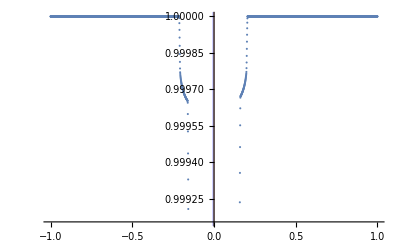

```mathematica
j=1;ListPlot[Subscript[mini, j][[All,{1,5}]],GridLines->{{{Subscript[tmiddy, j],Red},Pdays Round[(Median[Subscript[gini, j][[All,1]]]-τ0)/Pdays]+τ0,{Subscript[ttvmoon, j]/.Msp->Msptrue,Blue}},{}}]
```

### attempt a moon fold

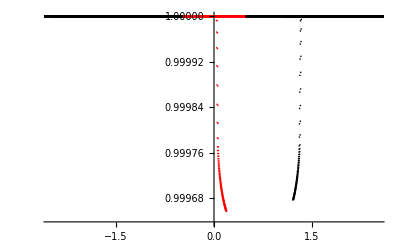

```mathematica
Mspgrid=Table[10^x,{x,-3,-1,0.1}];
k=0;Label[kloop];k=k+1;j=0;Label[jloop];j=j+1;Subscript[inmoon, j]=Select[Subscript[mini, j][[All,{1,5}]],((Subscript[ttvmoon, j]/.Msp->Mspgrid[[k]])-0.49μdur<#[[1]]<(Subscript[ttvmoon, j]/.Msp->Mspgrid[[k]])+0.49μdur)&&!(Subscript[tmiddy, j]-0.51μdur<#[[1]]<Subscript[tmiddy, j]+0.51μdur)&];Subscript[inmoon, j]=Table[{(Subscript[inmoon, j][[i,1]]-(Subscript[ttvmoon, j]/.Msp->Mspgrid[[k]]))/μdur,Subscript[inmoon, j][[i,2]]},{i,1,Length[Subscript[inmoon, j]]}];Subscript[outmoon, j]=Select[Subscript[mini, j][[All,{1,5}]],!((Subscript[ttvmoon, j]/.Msp->Mspgrid[[k]])-0.49μdur<#[[1]]<(Subscript[ttvmoon, j]/.Msp->Mspgrid[[k]])+0.49μdur)&&!(Subscript[tmiddy, j]-0.51μdur<#[[1]]<Subscript[tmiddy, j]+0.51μdur)&];Subscript[outmoon, j]=Table[{(Subscript[outmoon, j][[i,1]]-(Subscript[ttvmoon, j]/.Msp->Mspgrid[[k]]))/μdur,Subscript[outmoon, j][[i,2]]},{i,1,Length[Subscript[outmoon, j]]}];If[j<Length[epochs],Goto[jloop]];inmoonall=Flatten[Table[Subscript[inmoon, j],{j,1,Length[epochs]}],1];outmoonall=Flatten[Table[Subscript[outmoon, j],{j,1,Length[epochs]}],1];
μinmoon=Mean[inmoonall[[All,2]]];μoutmoon=Mean[outmoonall[[All,2]]];Subscript[δ, k]=μoutmoon-μinmoon;
ListPlot[{inmoonall,outmoonall},PlotStyle->{Red,Black},PlotRange->{{-2.5,2.5},All}]
```

```mathematica
Mspgrid=Table[10^x,{x,-3,0,0.01}];
k=0;Label[kloop];k=k+1;j=0;Label[jloop];j=j+1;Subscript[inmoon, j]=Select[Subscript[mini, j][[All,{1,5}]],((Subscript[ttvmoon, j]/.Msp->Mspgrid[[k]])-0.49μdur<#[[1]]<(Subscript[ttvmoon, j]/.Msp->Mspgrid[[k]])+0.49μdur)&&!(Subscript[tmiddy, j]-0.51μdur<#[[1]]<Subscript[tmiddy, j]+0.51μdur)&];Subscript[inmoon, j]=Table[{(Subscript[inmoon, j][[i,1]]-(Subscript[ttvmoon, j]/.Msp->Mspgrid[[k]]))/μdur,Subscript[inmoon, j][[i,2]]},{i,1,Length[Subscript[inmoon, j]]}];Subscript[outmoon, j]=Select[Subscript[mini, j][[All,{1,5}]],!((Subscript[ttvmoon, j]/.Msp->Mspgrid[[k]])-0.49μdur<#[[1]]<(Subscript[ttvmoon, j]/.Msp->Mspgrid[[k]])+0.49μdur)&&!(Subscript[tmiddy, j]-0.51μdur<#[[1]]<Subscript[tmiddy, j]+0.51μdur)&];Subscript[outmoon, j]=Table[{(Subscript[outmoon, j][[i,1]]-(Subscript[ttvmoon, j]/.Msp->Mspgrid[[k]]))/μdur,Subscript[outmoon, j][[i,2]]},{i,1,Length[Subscript[outmoon, j]]}];If[j<Length[epochs],Goto[jloop]];inmoonall=Flatten[Table[Subscript[inmoon, j],{j,1,Length[epochs]}],1];outmoonall=Flatten[Table[Subscript[outmoon, j],{j,1,Length[epochs]}],1];μinmoon=Mean[inmoonall[[All,2]]];μoutmoon=Mean[outmoonall[[All,2]]];Subscript[δ, k]=μoutmoon-μinmoon;If[k<Length[Mspgrid],Goto[kloop]];
result=Table[{Mspgrid[[k]],Subscript[δ, k]},{k,1,Length[Mspgrid]}];
```

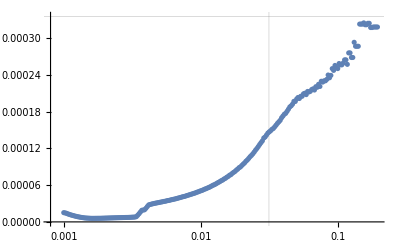

```mathematica
ListLogLinearPlot[result,GridLines->{{Msptrue},{strue^2}},PlotRange->{All,{All,strue^2}}]
```

```mathematica
temp=Select[result,NumberQ[#[[2]]]&];
temp=Table[{temp[[i,1]],temp[[i,2]],temp[[i,2]]/strue^2},{i,1,Length[temp]}];
Export[StringJoin[NotebookDirectory[],"Msp_grid.dat"],temp,"Table"]
```

/Users/davidkipping/Storage1/Work/Documents/Transit_Work/PAPERS/MoonFold/simulate/Jup-Super/f0.1/Msp_grid.dat